```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCComparisons`
<<GDCAnalysis3`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/AUS/GDC_CHP_AR_AUS_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/AUS/GDC_CHP_BR_AUS_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.}

{-1.,-1.}

{-1,-1}

```mathematica
tsAR={6,7,8};
tsBR={6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "AUS", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "AUS", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "AUS", "F"]
```

{{6,0.0606061},{6.5,0.0162602},{7,0.2},{7.5,0.2},{8,1.}}

{{6,0.0588873},{6.5,0.0144515},{7,0.198529},{7.5,0.198523},{8,1.}}

{{6,0.971848},{6.5,0.895546},{7,0.985399},{7.5,0.985339},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/AUS/AUS_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/AUS/AUS_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/AUS/AUS_F.txt"]
```

{{6,0.0606061},{6.5,0.0162602},{7,0.2},{7.5,0.2},{8,1.}}

{{6,0.0588733},{6.5,0.0144362},{7,0.198517},{7.5,0.19851},{8,1.}}

{{6,0.944408},{6.5,0.798284},{7,0.985277},{7.5,0.985212},{8,1}}

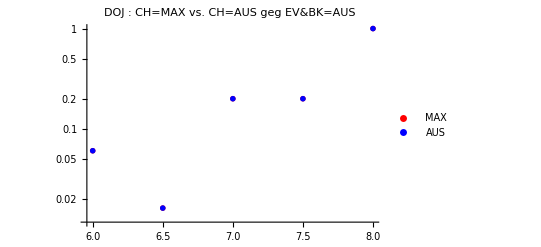
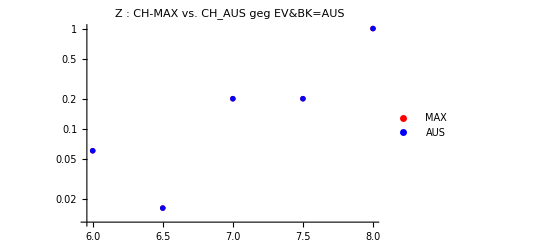
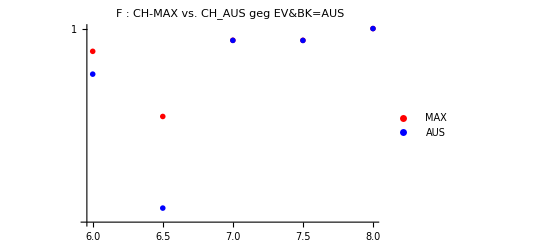

```mathematica
dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "AUS"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=AUS geg EV&BK=AUS",PlotMarkers->{{"X",12}, {"A",12}},ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "AUS"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_AUS geg EV&BK=AUS",PlotMarkers->{{"X",12}, {"A",12}},ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "AUS"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_AUS geg EV&BK=AUS",PlotMarkers->{{"X",12}, {"A",12}},ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]
```

```mathematica
(* dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]
Map[compCHMaxFunc[First[persMixFunc["AUS"]], #, tatCH , dojBR]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["AUS"]],# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["AUS"]],# , dojBR,  "CH", "PEN"]&,{4.5}]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["AUS"]]
```

19

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,tsAR]
```

{{6,0.866667},{7,0.866667},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR,persInd];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,persInd];
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR,persInd];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV];
fVVHist=vvHistPointsFunc[fVV];
```

5

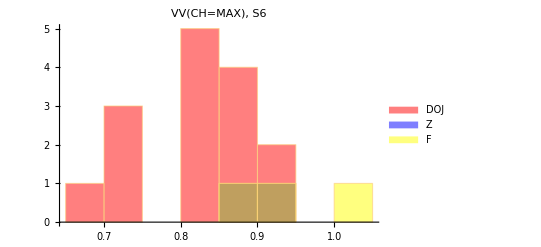
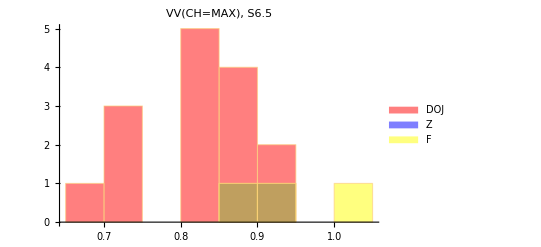
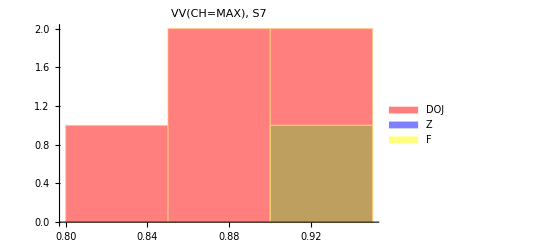
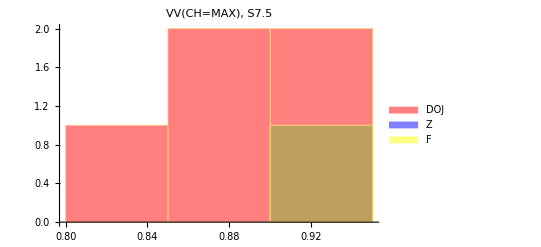
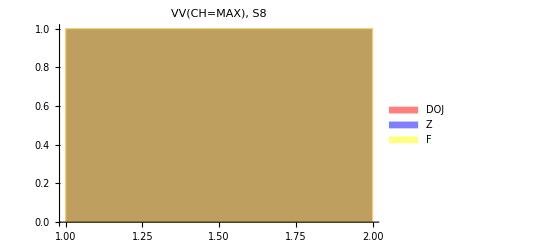
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=AUS",PlotMarkers->{{"D",12}}, PlotRange->All]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=AUS",PlotMarkers->{{"Z",12}}, PlotRange->All]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=AUS",PlotMarkers->{{"F",12}}, PlotRange->All]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=AUS",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;5]]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/AUS/"];
Export["COMP_DOJ_CHTAT_CHMAX_AUS.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_AUS.jpeg",confMAX,ImageResolution->300]
Export["VV_CHMAX_HIST_AUS.jpeg",histOut,ImageResolution->300]
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_AUS.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_AUS.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_AUS.txt"]
```

COMP_DOJ_CHTAT_CHMAX_AUS.jpeg

COMP_CHTAT_CHMAX_AUS.jpeg

VV_CHMAX_HIST_AUS.jpeg